# Trabalho Individual(Opcional) Lei de Coulomb

## Fundamentos de Física 3 - 2023/2 Aluno Caio Cordeiro Jácome

## Questão 2 - Duas partículas, com cargas elétricas q1 = q2 = 3, 20 × 10−19C estão ao longo do eixo y, sendo y1 = d = +1, 0m e y2 = −d = −1, 0m. Uma terceira partícula, com carga q3 = −1, 60 × 10−19C, esta situada ao longo do eixo x, com x podendo variar entre 0, 0 m e d = +1, 0 m.Para qual valor de x a soma das forcas eletrostáticas sobre q3 é mínima em modulo ? E máxima ? - calcular numericamente via Wolfram Mathematica o módulo da força, F(d), entre os 2 elétrons, para os valores numéricos dados; - fazer via Wolfram Mathematica um gráfico do módulo da força, F(d) x d, variando d entre 0 nm e 1 nm, com título e nomes dos eixos.

#### Calculando numericamente o módulo das forças entre os elétrons q1, q2 e q3; Temos:

q_1=q_2= 3,20 X 10^-19 C, q_3 = -1,60 X 10^-19 C

y_1 = +d = 1,0m , y_2= -d = -1,0m , 

k=8.99 X 10^-9  N·m^2/C^2= 1/(4πξ)
|F|= K  (q_1 X q_2)/r^2

2.30144×10^-28

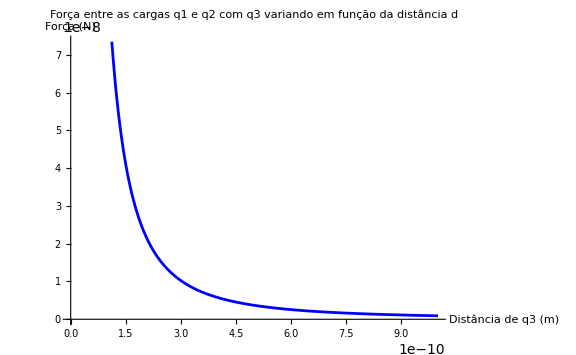

Syntax::sntxb: Expression cannot begin with "[q1*q2]/(r^2)".

Syntax::tsntxi: "(*Forçaqueq2incideemq1*" is incomplete; more input is needed.

Syntax::sntxb: Expression cannot begin with "[q1*q2]/(distanceBetweenQ1Q2^2)".

Power::infy: Infinite expression 1/0. encountered.

```mathematica
k=8.99*10^9;  (*Constante eletrostática em N·m^2/C^2*)
q1=3.20*10^-19; 
q2=3.20*10^-19; 
y1 = 1;
y2 = -1;
r = Abs[y1]+ Abs[y2];

forceQ=k* Abs[q1*q2/(r^2)]; (*Força que q2 incide em q1*)
Print[forceQ]

distanceQ3=Range[0,1*10^-9,0.01*10^-9];  (*Valores de d de 0 a 1 nm com incrementos de 0,01 nm*)
F[d_]:=Abs[(k*q1*q3)/distanceQ3^2]+Abs[(k*q2*q3)/distanceQ3^2]

(*Cria o gráfico*)
Plot[F[d_],{distanceQ3,0,1*10^-9},AxesLabel->{"Distância de q3 (m)","Força (N)"},PlotLabel->"Força entre as cargas q1 e q2 com q3 variando em função da distância d",PlotStyle->Blue, ImageSize->Large]
```